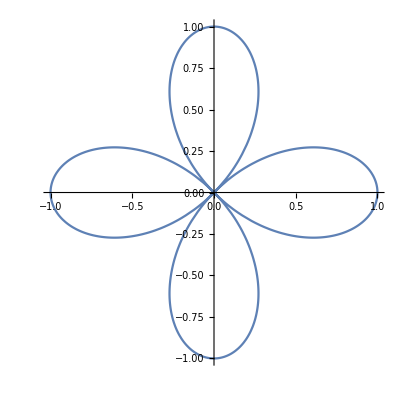

```mathematica
(* Rosa de cuatro pétalos *)
ParametricPlot[{Cos[2*u]*Cos[u],Cos[2*u]*Sin[u]},{u,0,2 Pi}]
```

```mathematica
(* Cilindro de la rosa de cuatro pétalos *)
ParametricPlot3D[{Cos[2 u] Cos[u],Cos[2 u] Sin[u],v},{u,0,2 π},{v,0,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-

```mathematica
(* Cono de la rosa de cuatro pétalos *)
ParametricPlot3D[{v*Cos[2 u] * Cos[u],v*Cos[2 u] * Sin[u], v},{u,0,2 π},{v,0,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

```mathematica
-Graphics3D-
(* Conoide de Wallis con a=b=c=1 *)
ParametricPlot3D[{v*Cos[u],v*Sin[u], Sqrt[1-Cos[u]^2]},{u,0,2 π},{v,0,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

```mathematica
-Graphics3D-
(* Conoide de Wallis con a=c=1, b=0.5 *)
a = 1;
b= 0.5;
c = 1
ParametricPlot3D[{v*Cos[u],v*Sin[u], c*Sqrt[a^2-b^2Cos[u]^2]},{u,0,2 π},{v,0,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]


(* Conoide de Plücker con n=2 *)
ParametricPlot3D[{v*Cos[u],v*Sin[u], Sin[2*u]},{u,0,2 π},{v,0,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-

1

-Graphics3D-

1

-Graphics3D-

```mathematica
(* Conoide de Plücker generalizado *)
n = 3;
ParametricPlot3D[{v*Cos[u],v*Sin[u], Sin[n*u]},{u,0,2 π},{v,0,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-

```mathematica
(* Banda de Möebius *)
ParametricPlot3D[{(1+v/2*Cos[u/2])*Cos[u],(1+v/2*Cos[u/2])Sin[u], v/2*Sin[u/2]},{u,0,2 π},{v,-1,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-

```mathematica
(* Helicoide *)
ParametricPlot3D[{v*Cos[u],v*Sin[u], u},{u,0,2 π},{v,0,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

```mathematica
-Graphics3D-
(* Paraguas de Whitney *)
ParametricPlot3D[{u*v,u, v^2},{u,-1,1},{v,-1,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-

```mathematica
(* Hiperboloide con a = b = c = 1 *)
ParametricPlot3D[{Cosh[u]*Cos[v],Cosh[u]*Sin[v], Sinh[u]},{u,-1,1},{v,0,2*Pi},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-

```mathematica
(* Esfera centrada en el punto (0,0,0) *)
SphericalPlot3D[{1},{θ,0,Pi},{ϕ,0,2Pi},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

```mathematica
-Graphics3D-

(* Plano *)
ParametricPlot3D[{6−6u−6v,−3u, 2v},{u,0,1},{v,0,3},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-

```mathematica
(* Cilindro *)
```

```mathematica
ParametricPlot3D[{Cos[u],Sin[u], v},{u,0,2Pi},{v,0,3},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-

ParametricPlot3D::plld: Endpoints for v in {v, -1, -1} must have distinct machine-precision numerical values.

```mathematica
(* Conoide de Plücker generalizado *)
n = 5;
ParametricPlot3D[{v*Cos[u],v*Sin[u], Sin[n*u]},{u,0,2 π},{v,0,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-

```mathematica
(* Paraguas de Whitney *)
ParametricPlot3D[{u*v,u, v^2},{u,-1,1},{v,-1,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-

```mathematica
(* Paraboloide hiperbólico *)

ParametricPlot3D[{u,v,u^2-v^2},{u,0,1},{v,0,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-

```mathematica
(* Cola de milano *)
ParametricPlot3D[{v,-4u^3 - 2*u*v,3*u^4 + v*u^2},{u,-1,1},{v,-2,2},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-